```mathematica
e=Import["Dropbox/quantum resonant/Eigen_fac_27_27_Z_barKernel.txt",{"List"}]//InputForm;
```

```mathematica
pnm=Length[e[[1]]]
```

574

```mathematica
Δ=Round[N[√pnm]]
```

24

```mathematica
sraw={};
```

```mathematica
For[i=Δ+1,i≤ pnm-Δ,i++,AppendTo[sraw,(e[[1,i+1]]-e[[1,i]])/(e[[1,i+Δ]]-e[[1,i-Δ]])]]
```

```mathematica
Length[sraw]
```

526

```mathematica
Total[sraw]
```

10.6588

```mathematica
savg=Total[sraw]/(pnm-2Δ)
```

0.0202639

```mathematica
s=sraw/savg;
```

```mathematica
ρP[x_]:=Exp[-x];ρW[x_]:=(π x)/2 Exp[-π x^2/4];
```

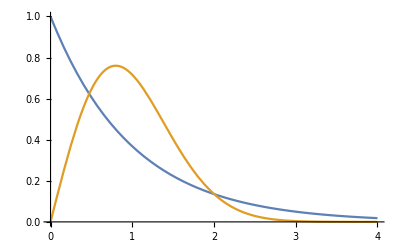

```mathematica
p1=Plot[{ρP[x],ρW[x]},{x,0,4}]
```

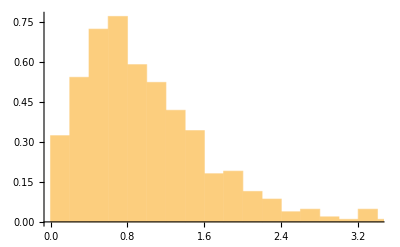

```mathematica
p2=Histogram[s,Automatic,"ProbabilityDensity"]
```

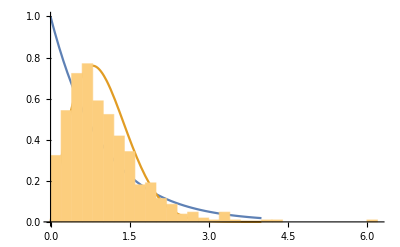

```mathematica
Show[{p1,p2},PlotLegends->p1,PlotRange->All]
```

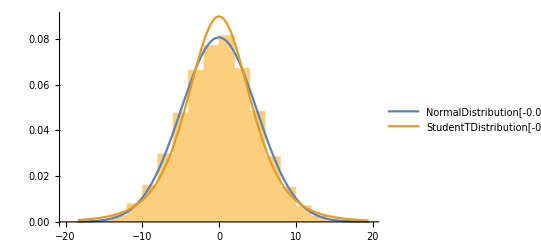

```mathematica
data=RandomVariate[NormalDistribution[0,5],10^4];
dist={EstimatedDistribution[data,NormalDistribution[mu,sigma]],EstimatedDistribution[data,StudentTDistribution[mu,sigma,5]]};
pdfs=PDF[#,x]&/@dist;
Show[{Histogram[data,Automatic,"ProbabilityDensity"],Plot[pdfs,{x,Min[data],Max[data]},PlotLegends->dist]}]
```